```mathematica
m0:=({{Cos[2 π νx]-wx vx Sin[2 π νx], wx^2 Sin[2 π νx], 0, 0}, {-(vx^2+1/wx^2)Sin[2 π νx], Cos[2 π νx]+wx vx Sin[2 π νx], 0, 0}, {0, 0, Cos[2 π νy]-wy vy Sin[2 π νy], wy^2 Sin[2 π νy]}, {0, 0, -(vy^2+1/wy^2)Sin[2 π νy], Cos[2 π νy]+wy vy Sin[2 π νy]}})
```

```mathematica
mq:=({{1, 0, 0, 0}, {0, 1, q, 0}, {0, 0, 1, 0}, {q, 0, 0, 1}})
```

```mathematica
s4:=({{0, 1, 0, 0}, {-1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, -1, 0}})
```

```mathematica
m=FullSimplify[mq.m0];
```

```mathematica
mmi=FullSimplify[m-s4.Transpose[m].s4];
```

```mathematica
ch=FullSimplify[Det[mmi-z IdentityMatrix[4]]]
```

((-z+2 Cos[2 π νx]) (z-2 Cos[2 π νy])+q^2 wx^2 wy^2 Sin[2 π νx] Sin[2 π νy])^2

```mathematica
cosmu1=FullSimplify[Eigenvalues[mmi]]
```

{Cos[2 π νx]+Cos[2 π νy]-(√(2+Cos[4 π νx]-4 Cos[2 π νx] Cos[2 π νy]+Cos[4 π νy]+2 q^2 wx^2 wy^2 Sin[2 π νx] Sin[2 π νy]))/(√2),Cos[2 π νx]+Cos[2 π νy]-(√(2+Cos[4 π νx]-4 Cos[2 π νx] Cos[2 π νy]+Cos[4 π νy]+2 q^2 wx^2 wy^2 Sin[2 π νx] Sin[2 π νy]))/(√2),Cos[2 π νx]+Cos[2 π νy]+(√(2+Cos[4 π νx]-4 Cos[2 π νx] Cos[2 π νy]+Cos[4 π νy]+2 q^2 wx^2 wy^2 Sin[2 π νx] Sin[2 π νy]))/(√2),Cos[2 π νx]+Cos[2 π νy]+(√(2+Cos[4 π νx]-4 Cos[2 π νx] Cos[2 π νy]+Cos[4 π νy]+2 q^2 wx^2 wy^2 Sin[2 π νx] Sin[2 π νy]))/(√2)}

```mathematica
FullSimplify[(2+Cos[4 π νx]-4 Cos[2 π νx] Cos[2 π νy]+Cos[4 π νy]+2 q^2 wx^2 wy^2 Sin[2 π νx] Sin[2 π νy])/2-(Cos[2 π νx]-Cos[2 π νy])^2]
```

q^2 wx^2 wy^2 Sin[2 π νx] Sin[2 π νy]

```mathematica
z1=Cos[2 π νx]+Cos[2 π νy]-Sqrt[(Cos[2 π νx]-Cos[2 π νy])^2+q^2 wx^2 wy^2 Sin[2 π νx] Sin[2 π νy]]
```

Cos[2 π νx]+Cos[2 π νy]-√((Cos[2 π νx]-Cos[2 π νy])^2+q^2 wx^2 wy^2 Sin[2 π νx] Sin[2 π νy])

```mathematica
z2=Cos[2 π νx]+Cos[2 π νy]+Sqrt[(Cos[2 π νx]-Cos[2 π νy])^2+q^2 wx^2 wy^2 Sin[2 π νx] Sin[2 π νy]]
```

Cos[2 π νx]+Cos[2 π νy]+√((Cos[2 π νx]-Cos[2 π νy])^2+q^2 wx^2 wy^2 Sin[2 π νx] Sin[2 π νy])

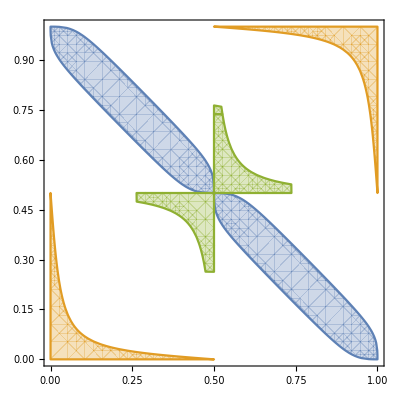

```mathematica
RegionPlot[{(Cos[2 π νx]-Cos[2 π νy])^2+0.3Sin[2 π νx] Sin[2 π νy]<0,2-Abs[Cos[2 π νx]+Cos[2 π νy]+Sqrt[(Cos[2 π νx]-Cos[2 π νy])^2+0.3 Sin[2 π νx] Sin[2 π νy]]]<0,2-Abs[Cos[2 π νx]+Cos[2 π νy]-Sqrt[(Cos[2 π νx]-Cos[2 π νy])^2+0.3 Sin[2 π νx] Sin[2 π νy]]]<0}, {νx,0,1},{νy,0,1}]
```

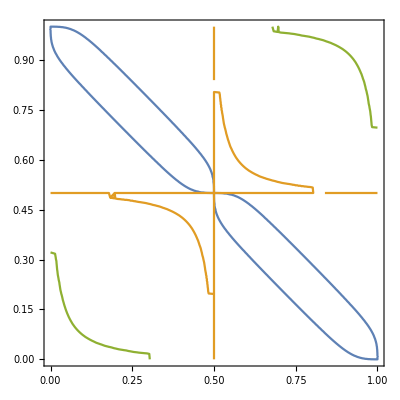

```mathematica
ContourPlot[{(Cos[2 π νx]-Cos[2 π νy])^2+0.3Sin[2 π νx] Sin[2 π νy], 2-Abs[(Cos[2 π νx]+Cos[2 π νy]-Sqrt[(Cos[2 π νx]-Cos[2 π νy])^2+0.3 Sin[2 π νx] Sin[2 π νy]])],2-Abs[Cos[2 π νx]+Cos[2 π νy]+Sqrt[(Cos[2 π νx]-Cos[2 π νy])^2+0.3 Sin[2 π νx] Sin[2 π νy]]]},{νx,0,1},{νy,0,1}]
```

```mathematica
num={νy-> .17, q-> .5, wx-> 1, wy-> 1};
```

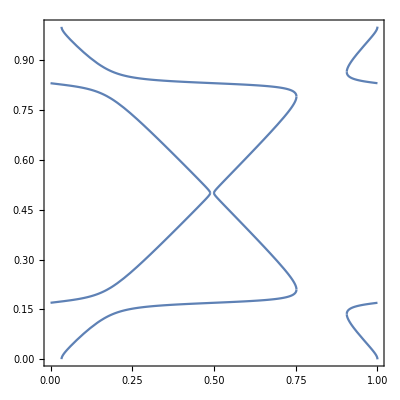

```mathematica
Plot[({2 π-ArcCos[{z1,z2}],ArcCos[{z1,z2}]}/(2 π))/.num,{νx,0,1},AspectRatio->1,Frame->True]
```

```mathematica
num = {νy-> .3, q-> .5, νx->.29, wy->.5};
```

```mathematica
x=FullSimplify[Eigenvectors[mmi /.{νy-> .17, q-> .5, wx-> 1, wy-> 1,νx->.16, vx->1,vy->1}]]
```

{{0.742179,0.,0.666993,0.0654977},{0.156608,0.732146,0.140743,0.647786},{0.103128,-0.665875,-0.119099,0.72924},{0.652803,0.,-0.753901,-0.0740319}}

```mathematica
Solve[(a x[[1]]).s4.(a x[[1]])==2i , a]
```

{}

```mathematica
cosm1=Cos[μ] Cos[δ] Cos[ϕ]-√(Sin[μ]^2(1-Cos[δ]^2 Cos[ϕ]^2)+d^2 Sin[μ+δ]Sin[μ-δ]  Sin[ϕ]^2);cosm2=Cos[μ] Cos[δ] Cos[ϕ]+√(Sin[μ]^2(1-Cos[δ]^2 Cos[ϕ]^2)+d^2 Sin[μ+δ]Sin[μ-δ]  Sin[ϕ]^2);
```

```mathematica
podint = Sin[μ]^2(1-Cos[δ]^2 Cos[ϕ]^2)+d^2 Sin[μ+δ]Sin[μ-δ]  Sin[ϕ]^2;
```

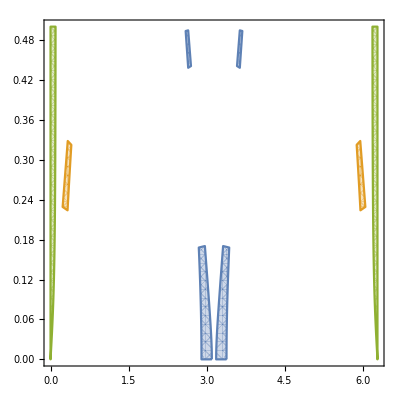

```mathematica
RegionPlot[{(1-Abs[cosm1/.{ϕ->.1, d->1}])<0, (1-Abs[cosm2/.{ϕ->.1, d->1}])<0, (podint/.{ϕ->.1, d->1})<0},{μ,0,2 π}, {δ,0,.5}]
```